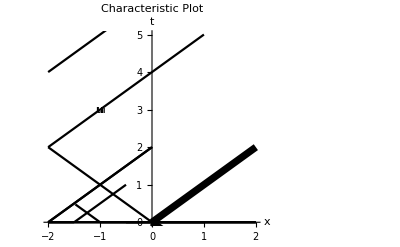

```mathematica
ul = 1;
um = 0;
ur = -1;
sm = (ul + um)/2;
a=-2;
b =2;
fl[x_,s_] := Piecewise[{{x/ul+s, x/ul+s≥x/sm+2&& x/ul+s ≥0}, {0, True}}]
fr[x_,s_] := Piecewise[{{x/ur+s, x/ur+s<=x/ur && x/ur+s ≥0}, {0, True}}]
Show[Table[Plot[fl[x,s],{x,a,0},PlotStyle->Black],{s,1,2,.5}],Table[Plot[fl[x,s],{x,a,1},PlotStyle->Black],{s,2,6,2}],
Table[Plot[fr[x,s],{x,a,b},PlotStyle->Black],{s,-2,0,1}],Plot[{x/ul,x/ur},{x,0,b},PlotStyle->Directive[Black,Thickness[.013]]],Graphics[{Text[Style["u_l",Bold,Large],{-1,3}],Text[Style["u_m",Bold,Large],{2.3,4}],Text[Style["x / t",Bold,Large],{5,3}],Text[Style["u_r",Bold,Large],{5.5,1.5}]}],PlotRange->{{a,b},{0,5}},AxesLabel->{Style["x",Medium,Bold],Style["t",Medium,Bold]},PlotLabel->Style["Characteristic Plot",Large],Frame->False, Axes->True]
```

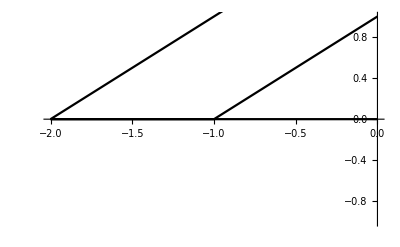

```mathematica
Show[Table[Plot[fl[x,s],{x,a,0},PlotStyle->Black],{s,0,2,1}]]
```

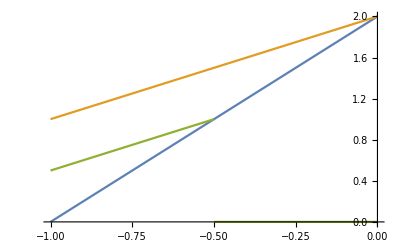

```mathematica
Plot[{2x+2,fl[x,2],fl[x,1.5]},{x,-1,0}]
```

```mathematica
fl[x,1.5]
```

Piecewise[{{1.5+x, 1.5+x≥2 x&&1.5+x≥0}, {0, True}}]

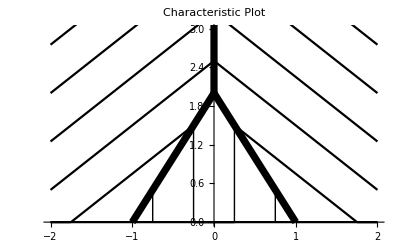

```mathematica
ul = 1;
um = 0;
ur = -1;
sm = (ul + um)/2;
sr = (ur+um)/2;
a=-2;
b =2;
fl[x_,s_] := Piecewise[{{x/ul+s, x/ul+s≥x/sm+2&& x/ul+s ≥0}, {0, True}}];
fm[x_,s_]:=Piecewise[{{□, □}, {□, □}}];
fr[x_,s_] := Piecewise[{{x/ur+s, x/ur+s≥x/sr+2&& x/ur+s ≥0}, {0, True}}];
Show[Table[Plot[fl[x,s],{x,-2,0},PlotStyle->Black],{s,1,6,.75}],
Table[Plot[fr[x,s],{x,0,2},PlotStyle->Black],{s,1,6,.75}],
Plot[{x/sm+2},{x,-1,0},PlotStyle->Directive[Black,Thickness[.013]]],
Plot[{x/sr+2},{x,0,1},PlotStyle->Directive[Black,Thickness[.013]]],
Graphics[{Thick,Black,Line[{{{-.75,0},{-.75,.5}},{{-.25,0},{-.25,1.5}},{{.75,0},{.75,.5}},{{.25,0},{.25,1.5}}}],Thickness[.013], Black,Line[{{0,2},{0,4}}]}],
PlotLabel->Style["Characteristic Plot",Large],Frame->False, Axes->True,PlotRange->{0,3}]
```

```mathematica
ContourPlot[Table[x==s,{s,-1,1,.5}],{x,-2,2},{t,0,3}]
```

-Graphics-

```mathematica
Table[x==s,{s,-1,1,.5}]
```

{x==-1.,x==-0.5,x==0.,x==0.5,x==1.}

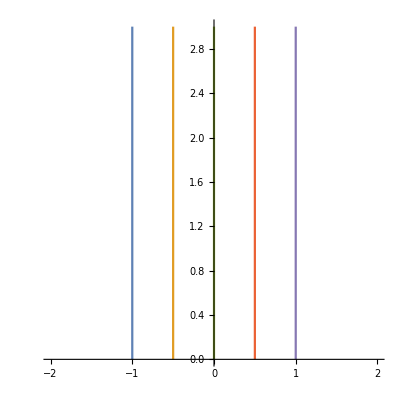

```mathematica
ContourPlot[{x==-1.,x==-0.5,x==0.,x==0.5,x==1.},{x,-2,2},{t,0,3},Frame->False,Axes->True]
```

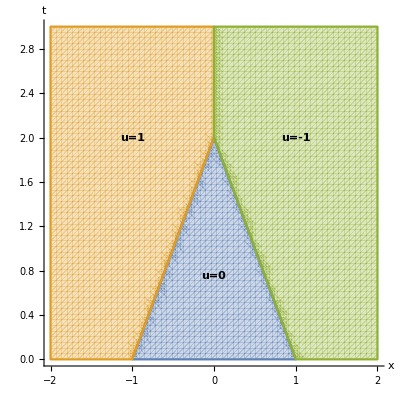

```mathematica
a =-2;
b=2;
tMax = 3;
Show[RegionPlot[{t>0&&t<2x+2&&t<-2x + 2,t>0&&t>2x+2&&t<2||t>2&&x<0,t>0&&t>-2x+2&&t<2||t>2&&x>0},{x,a,b},{t,0,tMax},PlotPoints->60],Graphics[{Text[Style["u=1",Bold,Large],{-1,2}],Text[Style["u=0",Bold,Large],{0,.75}],Text[Style["u=-1",Bold,Large],{1,2}]}],PlotRange->{{a,b},{0,tMax}},AxesLabel->{Style["x",Large,Bold],Style["t",Large,Bold]},Axes->True,Frame->False,AxesStyle->{12,Bold}]
```

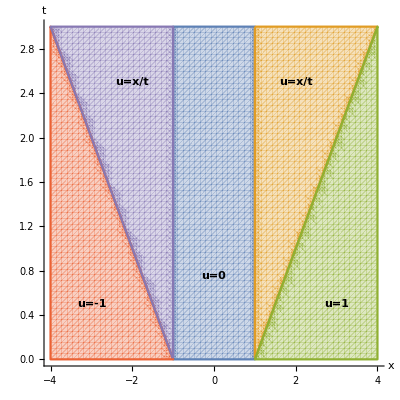

```mathematica
a =-4;
b=4;
tMax = 3;
Show[RegionPlot[{x>-1&& x< 1,x>1 && x<t+1,x>t+1,x<-t-1,x>-t-1&&x<-1},{x,a,b},{t,0,tMax},PlotPoints->60],Graphics[{Text[Style["u=1",Bold,Large],{3,.5}],Text[Style["u=0",Bold,Large],{0,.75}],Text[Style["u=-1",Bold,Large],{-3,.5}],Text[Style["u=x/t",Bold,Large],{-2,2.5}],Text[Style["u=x/t",Bold,Large],{2,2.5}]}],PlotRange->{{a,b},{0,tMax}},AxesLabel->{Style["x",Large,Bold],Style["t",Large,Bold]},Axes->True,Frame->False,AxesStyle->{12,Bold}]
```

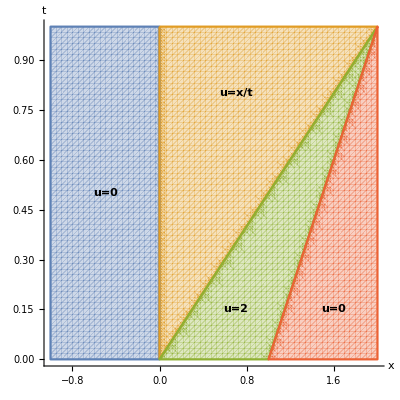

```mathematica
a =-1;
b=2;
tMax = 1;
Show[RegionPlot[{x < 0, 0 < x < 2t, 2t < x < t + 1, t + 1 < x},{x,a,b},{t,0,tMax},PlotPoints->60],Graphics[{Text[Style["u=0",Bold,Large],{-.5,.5}],Text[Style["u=x/t",Bold,Large],{.7,.8}],Text[Style["u=2",Bold,Large],{.7,.15}],Text[Style["u=0",Bold,Large],{1.6,.15}]}],PlotRange->{{a,b},{0,tMax}},AxesLabel->{Style["x",Large,Bold],Style["t",Large,Bold]},Axes->True,Frame->False,AxesStyle->{12,Bold}]
```